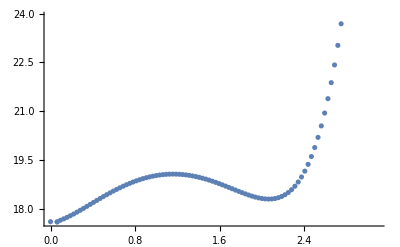

```mathematica
f4={{0,17.610224},{0.062500,17.603234},{0.062500,17.603234},{0.093750,17.653723},{0.125000,17.696613},{0.156250,17.742578},{0.187500,17.792407},{0.218750,17.845635},{0.250000,17.901589},{0.281250,17.959607},{0.312500,18.019085},{0.343750,18.079483},{0.375000,18.140325},{0.406250,18.201186},{0.437500,18.261691},{0.468750,18.321502},{0.500000,18.380316},{0.531250,18.437862},{0.562500,18.493895},{0.593750,18.548192},{0.625000,18.600551},{0.656250,18.650790},{0.687500,18.698742},{0.718750,18.744257},{0.750000,18.787197},{0.781250,18.827440},{0.812500,18.864874},{0.843750,18.899399},{0.875000,18.930925},{0.906250,18.959374},{0.937500,18.984677},{0.968750,19.006776},{1.000000,19.025621},{1.031250,19.041173},{1.062500,19.053404},{1.093750,19.062293},{1.125000,19.067832},{1.156250,19.070021},{1.187500,19.068872},{1.218750,19.064411},{1.250000,19.056672},{1.281250,19.045705},{1.312500,19.031572},{1.343750,19.014351},{1.375000,18.994136},{1.406250,18.971035},{1.437500,18.945180},{1.468750,18.916719},{1.500000,18.885823},{1.531250,18.852687},{1.562500,18.817532},{1.593750,18.780605},{1.625000,18.742187},{1.656250,18.702590},{1.687500,18.662162},{1.718750,18.621292},{1.750000,18.580410},{1.781250,18.539992},{1.812500,18.500566},{1.843750,18.462713},{1.875000,18.427072},{1.906250,18.394347},{1.937500,18.365306},{1.968750,18.340794},{2.000000,18.321731},{2.031250,18.309121},{2.062500,18.304055},{2.093750,18.307717},{2.125000,18.321390},{2.156250,18.346461},{2.187500,18.384423},{2.218750,18.436880},{2.250000,18.505556},{2.281250,18.592288},{2.312500,18.699038},{2.343750,18.827888},{2.375000,18.981045},{2.406250,19.160836},{2.437500,19.369710},{2.468750,19.610236},{2.500000,19.885100},{2.531250,20.197102},{2.562500,20.549163},{2.593750,20.944325},{2.625000,21.385763},{2.656250,21.876810},{2.687500,22.420996},{2.718750,23.022106},{2.750000,23.684273},{2.781250,24.412117},{2.812500,25.210930},{2.843750,26.086947},{2.875000,27.047693},{2.906250,28.102424},{2.937500,29.262621},{2.968750,30.542322},{3.000000,31.956748},{3.031250,33.515056},{3.062500,35.213050},{3.093750,36.944784}};
ListPlot[f4]
```

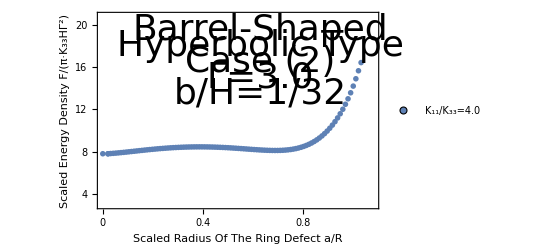

```mathematica
ee4=f4*Table[{1/3,4/9},{i,0,99}];
ListPlot[{ee4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{4,8,12,16,20},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.08},{3,20.8}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.63,19.5}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.63,18}],Text[Style["Case (2)",Directive[Black,36]],{0.63,16.5}],Text[Style["Γ=3.0",Directive[Black,36]],{0.63,15}],Text[Style["b/H=1/32",Directive[Black,36]],{0.63,13.5}]}]
```